GUÍA PARA RESOLVER ALGUNAS CUESTIONES DE FORMULAS

### Hecho por: Franzoi Valentin, 2023

## DATOS

```mathematica
Clear["Global`*"](* Alt + c + l*)
NN=7.5;(*CV HP*)
n=360(*RPM*);
(*LEWIS*)
Y=0.346;(* forma *)
M = 4;(*MODULO*)
sw=28; (*sigma w*)
k1=1.7;
ks=1.75;
kf=1.8;
(*DELTAP*)
c=0;(* error*)
cv=0.625;
(*BUCK*)
nabla =0.24;
cz=1.43;
Cpsi=1;
psi=(0*Pi)/180;(*PSI si eje recto 0*) 
cs=1.75;
```

## Diametros y módulo

```mathematica
a=1.8;
360*a
3000*a
```

```mathematica
M=4;
z1=24;
z2=54;
psi=0Pi/180;(*0 para rectos*)
```

```mathematica
{"Dp1"->M*z1/Cos[psi],"Dp2"->M*z2/Cos[psi],"De1"->(M*z1/Cos[psi])+2*M,"De2"->(M*z2/Cos[psi])+2*M}//N
```

```mathematica
Clear["Global`*"](* Alt + c + l*)
```

## Verificar Buckingham DELTA P

```mathematica
Clear["Global`*"](* Alt + c + l*)
```

#### Manipulate te permite variar dp para conocer el b mínimo necesario en una condición

```mathematica
Manipulate[{Solve[{(71620*NN*2*10)/(n*dp)+(6.8*Round[(n*2Pi*dp)/(60*2000),0.01]*Cos[psi]*((71620*NN*2*10)/(n*dp)+b*c  (Cos[psi])^2))/(6.8*Round[(n*2Pi*dp)/(60*2000),0.01]+√((71620*NN*2*10)/(n*dp)+b*c (Cos[psi])^2))==(dp*b*nabla*cz*Cpsi)/cs},b],vt->Round[(n*2Pi*dp)/(60*2000),0.01]//N,"dp"->dp//N},{dp,50,285}]
```

#### Valores de algunos datos que vamos a precisar / corroborar

```mathematica
{"pt"-> Round[(71620*NN*2*10)/(n*dp),0.01],"vt"->Round[(n*2Pi*dp)/(60*2000),0.01],"cos(psi)"->Cos[(psi*Pi)/180],"AP"->(6.8*Round[(n*2Pi*dp)/(60*2000),0.01]*Cos[psi]*(Round[(71620*NN*2*10)/(n*dp),0.01]+b*c  (Cos[psi])^2))/(6.8*Round[(n*2Pi*dp)/(60*2000),0.01]+√(Round[(71620*NN*2*10)/(n*dp),0.01]+b*c (Cos[psi])^2)),
"Pd"->Round[(71620*NN*2*10)/(n*dp),0.01]+(6.8*Round[(n*2Pi*dp)/(60*2000),0.01]*Cos[psi]*(Round[(71620*NN*2*10)/(n*dp),0.01]+b*c  (Cos[psi])^2))/(6.8*Round[(n*2Pi*dp)/(60*2000),0.01]+√(Round[(71620*NN*2*10)/(n*dp),0.01]+b*c (Cos[psi])^2)),"Fb"-> (dp*b*nabla*cz*Cpsi)/cs}/.
{dp->55.16,b->45}//N
```

#### Región donde se cumple

```mathematica
RegionPlot[{(71620*NN*2*10)/(n*dp)+(6.8*(n*2Pi*dp)/(60*2000)*Cos[(psi*Pi)/180]*((71620*NN*2*10)/(n*dp)+b*c  (Cos[(psi*Pi)/180])^2))/(6.8*(n*2Pi*dp)/(60*2000)+√((71620*NN*2*10)/(n*dp)+b*c (Cos[(psi*Pi)/180])^2))<(dp*b*nabla*cz*Cpsi)/cs,dp>63.2,b>41.6},{dp,0,200},{b,0,200},AxesLabel->{"dp","b"},Mesh->Full]
```

## Verificar LEWIS DELTA P

```mathematica
Clear["Global`*"](* Alt + c + l*)
```

#### Manipulate te permite variar dp para conocer el b mínimo necesario en una condición

```mathematica
Manipulate[{Solve[{(71620*NN*2*10)/(n*dp)+(6.8*Round[(n*2Pi*dp)/(60*2000),0.01]*Cos[psi]*((71620*NN*2*10)/(n*dp)+b*c  (Cos[psi])^2))/(6.8*Round[(n*2Pi*dp)/(60*2000),0.01]+√((71620*NN*2*10)/(n*dp)+b*c (Cos[psi])^2))==(b*Y*M*sw*k1)/(ks*kf)},b],vt->Round[(n*2Pi*dp)/(60*2000),0.01]//N,"dp"->dp},{dp,50,85}]
```

#### Valores de algunos datos que vamos a precisar / corroborar

```mathematica
{"fl"-> (b*Y*M*sw*k1)/(ks*kf),"pt"->Round[(71620*NN*2*10)/(n*dp),0.01],
"vt"-> Round[(n*2Pi*dp)/(60*2000),0.01],
"cos(psi)"->Cos[(psi*Pi)/180],
"AP"->(6.8*Round[(n*2Pi*dp)/(60*2000),0.01]*Cos[psi]*((71620*NN*2*10)/(n*dp)+b*c  (Cos[psi])^2))/(6.8*Round[(n*2Pi*dp)/(60*2000),0.01]+√((71620*NN*2*10)/(n*dp)+b*c (Cos[psi])^2)),
"Pd"-> Round[(71620*NN*2*10)/(n*dp),0.01]+(6.8*Round[(n*2Pi*dp)/(60*2000),0.01]*Cos[psi]*(Round[(71620*NN*2*10)/(n*dp),0.01]+b*c  (Cos[psi])^2))/(6.8*Round[(n*2Pi*dp)/(60*2000),0.01]+√(Round[(71620*NN*2*10)/(n*dp),0.01]+b*c (Cos[psi])^2))}/.
{dp->50,b->27}//N
```

#### Región donde se cumple

```mathematica
RegionPlot[{(71620*NN*2*10)/(n*dp)+(6.8*(n*2Pi*dp)/(60*2000)*Cos[(psi*Pi)/180]*((71620*NN*2*10)/(n*dp)+b*c  (Cos[(psi*Pi)/180])^2))/(6.8*(n*2Pi*dp)/(60*2000)+√((71620*NN*2*10)/(n*dp)+b*c (Cos[(psi*Pi)/180])^2))< (b*Y*M*sw*k1)/(ks*kf),dp>50,b>27},{dp,0,200},{b,0,200},AxesLabel->{"dp","b"},Mesh->Full]
```

## Verificar Buckingham

```mathematica
Clear["Global`*"](* Alt + c + l*)
```

#### Manipulate te permite variar dp para conocer el b mínimo necesario en una condición

```mathematica
Manipulate[{Solve[(71620*NN*2*10)/(n*dp)==(dp*b*nabla*cz*Cpsi*cv)/cs,b],"dp"->dp},{dp,50,85}]
```

#### Valores de algunos datos que vamos a precisar / corroborar

```mathematica
{"pt"->Round[ (71620*NN*2*10)/(n*dp),0.1],"vt"-> Round[(n*2Pi*dp)/(60*2000),0.1],"cos(psi)"->Cos[(psi*Pi)/180],"Fb"-> Round[(dp*b*nabla*cz*Cpsi)/cs,0.1]}/.
{dp->65,b->41.6}//N
```

#### Región donde se cumple

```mathematica
RegionPlot[{(71620*NN*2*10)/(n*dp)<(dp*b*nabla*cz*Cpsi*cv)/cs,dp>50,b>27},{dp,0,200},{b,0,200},AxesLabel->{"dp","b"},Mesh->Full]
```

## Verificar LEWIS

#### Manipulate te permite variar dp para conocer el b mínimo necesario en una condición

```mathematica
Clear["Global`*"](* Alt + c + l*)
```

```mathematica
Manipulate[{Solve[{(71620*NN*2*10)/(n*dp)==(b*Y*M*sw*cv*k1)/(ks*kf)},b]"dp"->dp,"vt"->(n*2Pi*dp)/(60*2000)},{dp,96,185}]//N
```

#### Valores de algunos datos que vamos a precisar / corroborar

```mathematica
{"fl"->Round[ (b*Y*M*sw*cv*k1)/(ks*kf),0.1],"pt"->Round[ (71620*NN*2*10)/(n*dp),0.1],"vt"->Round[ (n*2Pi*dp)/(60*2000),0.1]}/.
{dp->70,b->30}//N
```

#### Región donde se cumple

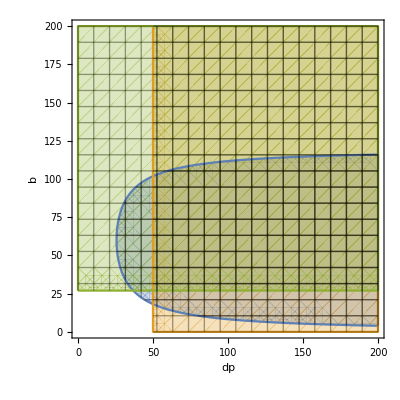

```mathematica
RegionPlot[{(71620*NN*2*10)/(n*dp)< b*Y*M*sw*((120-b)/120),dp>50,b>27},{dp,0,200},{b,0,200},AxesLabel->{"dp","b"},Mesh->Full]
```

## IGUALDADES

Delta P:

```mathematica
RegionPlot[{(71620*NN*2*10)/(n*dp)+(6.8*(n*2Pi*dp)/(60*2000)*Cos[psi]*((71620*NN*2*10)/(n*dp)+b*c  (Cos[psi])^2))/(6.8*(n*2Pi*dp)/(60*2000)+√((71620*NN*2*10)/(n*dp)+b*c (Cos[psi])^2))<(b*Y*M*sw*k1)/(ks*kf),(dp*b*nabla*cz*Cpsi)/cs>(71620*NN*2*10)/(n*dp)+(6.8*(n*2Pi*dp)/(60*2000)*Cos[psi]*((71620*NN*2*10)/(n*dp)+b*c  (Cos[psi])^2))/(6.8*(n*2Pi*dp)/(60*2000)+√((71620*NN*2*10)/(n*dp)+b*c (Cos[psi])^2))},{b,0,200},{dp,0,200},Mesh->Full]
```

CV:

```mathematica
RegionPlot[{(71620*NN*2*10)/(n*dp)<(b*Y*M*sw*k1*cv)/(ks*kf),(dp*b*nabla*cz*Cpsi*cv)/cs>(71620*NN*2*10)/(n*dp)},{b,0,200},{dp,0,200},Mesh->Full]
```

asd

## Verificar LEWIS CONO

#### Manipulate te permite variar dp para conocer el b mínimo necesario en una condición

```mathematica
Clear["Global`*"](* Alt + c + l*)
```

```mathematica
Manipulate[{Solve[{(71620*NN*2*10)/(n*dp)== b*Y*M*sw*((120-b)/120)},b]"dp"->dp,"vt"->(n*2Pi*dp)/(60*2000)},{dp,96,185}]//N
```

#### Valores de algunos datos que vamos a precisar / corroborar

```mathematica
{"fl"->Round[  b*Y*M*sw*((118.4-b)/118.4),0.1],"pt"->Round[ (71620*NN*2*10)/(n*dp),0.1],"vt"->Round[ (n*2Pi*dp)/(60*2000),0.1]}/.
{dp->96,b->30}//N
```

{fl→868.,pt→310.9,vt→1.8}

#### Región donde se cumple

```mathematica
RegionPlot[{(71620*NN*2*10)/(n*dp)< b*Y*M*sw*((120-b)/120),dp>50,b>27},{dp,0,200},{b,0,200},AxesLabel->{"dp","b"},Mesh->Full]
```

-Graphics-